```mathematica
SetDirectory["/home/leonard/Documents/Projects/PhysicalDistance/Codes/data/KickedRotor/"];
k=10.1;
m=10;
prefix="K="<>ToString[k]<>"_m="<>ToString[m];
savdSet=Import[prefix<>"/tLis.dat","Table"]//Flatten;
len=Length[savdSet];
stattabs=Import[prefix<>"/GrossStatTabs.txt","Table"];
qstatTabs=Table[#[[i]]&/@stattabs,{i,1,len}];
klstatTabs=Table[#[[i+3len]]&/@stattabs,{i,1,len}];
```

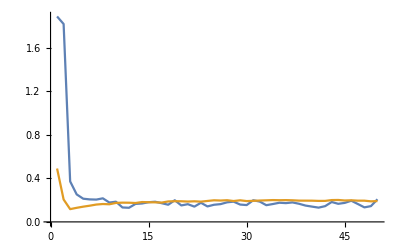

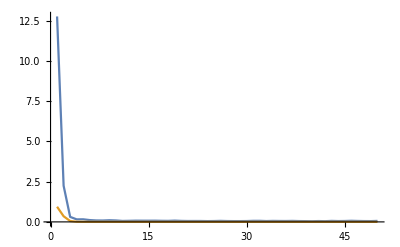

```mathematica
ListLinePlot[{qstatTabs[[;;,-1]],(Variance/@qstatTabs)/(Mean/@qstatTabs)},PlotRange->All]
ListLinePlot[{klstatTabs[[;;,-1]],(Variance/@klstatTabs)/(Mean/@klstatTabs)},PlotRange->All]
```

```mathematica
FileNames[]
```

{K=0.1_m=10,K=0.3_m=10,K=0.3_m=10.gaus,K=0.3_m=15,K=0.3_m=20,K=0.3_m=30_1,K=0.6_m=10,K=0.99_m=10,K=0.9_m=10,K=10.1_m=10,K=15.1_m=10,K=1.5_m=10,K=1.6_m=10,K=3.1_m=10,K=4.1_m=10,K=5.0_m=10,K=5.1_m=10,K=6.1_m=10}

```mathematica
tb=Table[
m=10;
prefix="K="<>ToString[k]<>"_m="<>ToString[m];
savdSet=Import[prefix<>"/tLis.dat","Table"]//Flatten;
len=Length[savdSet];
stattabs=Import[prefix<>"/GrossStatTabs.txt","Table"];
qstatTabs=Table[#[[i]]&/@stattabs,{i,1,len}];
klstatTabs=Table[#[[i+3len]]&/@stattabs,{i,1,len}];
{(Variance/@qstatTabs)/(Mean/@qstatTabs),(Variance/@klstatTabs)/(Mean/@klstatTabs)},{k,{0.3,0.6,0.9,0.99,1.5,3.1,4.1,5.1,6.1,10.1,15.1}}];
```

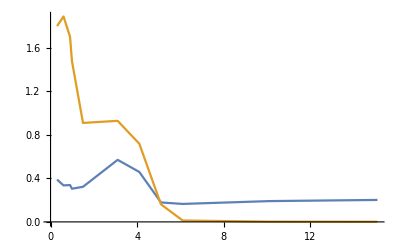

```mathematica
ListLinePlot[{Transpose[{{0.3,0.6,0.9,0.99,1.5,3.1,4.1,5.1,6.1,10.1,15.1},#[[1]][[-1]]&/@tb}],Transpose[{{0.3,0.6,0.9,0.99,1.5,3.1,4.1,5.1,6.1,10.1,15.1},#[[2]][[-1]]&/@tb}]}]
```